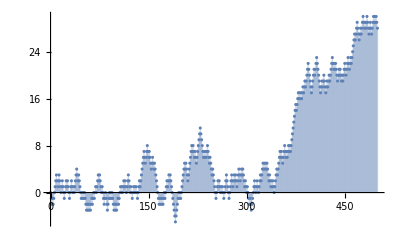

```mathematica
ListPlot[RandomFunction[RandomWalkProcess[.5],{0,500}],Filling->Axis]
```

```mathematica
Mean@RandomWalkProcess[.5][t]
Variance@RandomWalkProcess[.5][t]
```

0.

1. t

```mathematica
TransformedDistribution[2x-t,x\[Distributed]BinomialDistribution[t,p]]
```

TransformedDistribution[2 x-t,x\[Distributed]BinomialDistribution[t,p]]

模拟随机游走过程的500个路径：

```mathematica
SeedRandom[1234];
data=RandomFunction[RandomWalkProcess[.5],{100},500];
```

在50处取切片，并对其分布进行可视化：

```mathematica
sd=data["SliceData",100];
```

```mathematica
cf=ColorData["Rainbow"];
sliced=BarChart[Last[#],Axes->False,BarOrigin->Left,AspectRatio->4,ChartStyle->(cf/@Rescale[MovingAverage[First[#],2],{Min[sd],Max[sd]},{0,1}]),ImageSize->60]&[HistogramList[sd,{Range[Min[sd],Max[sd],(Max[sd]-Min[sd])/15]}]];
```

绘制50处切片分布的路径和直方图分布：

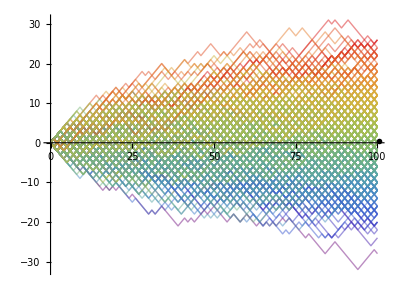

```mathematica
ListLinePlot[data,ImageSize->400,PlotRange->All,
AspectRatio->3/4,Epilog->Inset[sliced,{100.5,Mean[sd]},{0,8}],PlotStyle->(cf/@Rescale[sd]),BaseStyle->Directive[Thin,Opacity[0.5]],PlotRangePadding->{{0,20},{.5,7}}]
```

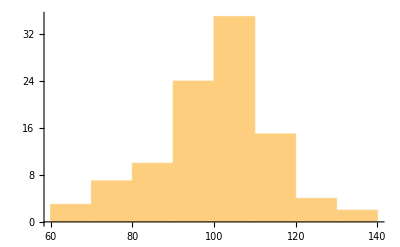

```mathematica
dist=100~Table~100;Do[m=RandomChoice@Position[dist,_?Positive];
p=RandomInteger@{1,100};dist[[m]]-=1;
dist[[p]]+=1,10000];Histogram@dist
```

```mathematica
dist=ConstantArray[100,100];Do[m=RandomChoice@SparseArray[Sign@dist]["NonzeroPositions"];
p=RandomInteger@{1,100};dist[[m]]-=1;
dist[[p]]+=1,10000];
Histogram@dist
```